# Elliptic Curve

### Author

Eric W. Weisstein
January 25, 2009

This notebook downloaded from http://mathworld.wolfram.com/notebooks/NumberTheory/EllipticCurve.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/EllipticCurve.html.

For a list of Eric's math packages that may be needed to evaluate this notebook, see Mathematica Information Center's MathSource item 4775.  A list of Eric's utility packages that may be needed to evaluate this notebook may be downloaded from MathSource item 5087.

©2009 Wolfram Research, Inc. except for portions noted otherwise

## Examples

#### V5

```mathematica
<<Graphics`ImplicitPlot`
<<Graphics`Colors`
```

```mathematica
curves={x^3-1,x^3+1,x^3-3x+3,x^3-4x,x^3-x};
```

```mathematica
Factor/@curves
```

{(-1+x) (1+x+x^2),(1+x) (1-x+x^2),3-3 x+x^3,(-2+x) x (2+x),(-1+x) x (1+x)}

```mathematica
Show[GraphicsArray[ImplicitPlot[#,{x,-3,3},
DisplayFunction->Identity,
PlotLabel->TraditionalForm[#],
PlotStyle->Red,AspectRatio->1,Ticks->None]&/@(y^2==#&/@curves)
]]
```

⁃GraphicsArray⁃

#### V7

```mathematica
curves={x^3-1,x^3+1,x^3-3x+3,x^3-4x,x^3-x};
```

```mathematica
Factor/@curves
```

{(-1+x) (1+x+x^2),(1+x) (1-x+x^2),3-3 x+x^3,(-2+x) x (2+x),(-1+x) x (1+x)}

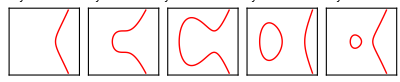

```mathematica
GraphicsGrid[{ContourPlot[#,{x,-3,3},{y,-3,3},PlotLabel->#,ContourStyle->Red,BaseStyle->9,FrameTicks->None,Axes->True,AspectRatio->1]&/@(y^2==#&/@curves)},ImageSize->400,Spacings->-15]
```